```mathematica
(*绘制y的曲线*)
```

```mathematica
a=Import["G:\\calc-online\\gpd\\k-result\\diagram-a-n.wdx"];
f1=(-I)*Query[1,1]@a;
g1=Query[1,2]@a;
f2=Query[2,1]@a;
g2=Query[2,2]@a;

nf1=f1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Q^2->1,q3->0.90494455,Λ->1};
ng1=g1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Q^2->1,q3->0.90494455,Λ->1};
nf2=f2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Q^2->1,q3->0.90494455,Λ->1};
ng2=g2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Q^2->1,q3->0.90494455,Λ->1};
```

```mathematica
(*研究一下，总不能自己手动一个点一个点写*)
ref1=Simplify[nf1/.{y->-0.15}];
```

```mathematica
NIntegrate[ref1,{k3,0,∞},{θ,0,2π},WorkingPrecision->10]
```

-3.285621616 ⅈ

```mathematica
ref1[x_]=Simplify[nf1/.{y->x}];
```

Set::write: Tag Times in ((0.+0.152639 ⅈ) k3 ((0.+9.86076×10^-32 ⅈ) (3.00608×10^28+«8»+7.73651×10^15 («2»)^(«2»))+«10»))/((0.0201632+1. k3^2+0.037706 k3 Cos[θ]) («1»)^2 («1») («1»)^2 («19»+1. («2»)^2+«1»)^2 («1»)^3)[x_] is Protected.

```mathematica
ref1[1]
```

-(((0.+1.79282×10^-13 ⅈ) k3 (-5.85492×10^16-3.00027×10^17 k3^2-9.17345×10^17 k3^4-1.60859×10^18 k3^6-1.53522×10^18 k3^8-7.76005×10^17 k3^10-1.92006×10^17 k3^12-1.82522×10^16 k3^14+298.129 k3^16+26.3616 k3^18+k3 (-2.44135×10^17-3.29284×10^18 k3^2-1.1021×10^19 k3^4-1.54445×10^19 k3^6-1.02831×10^19 k3^8-3.16647×10^18 k3^10-3.6281×10^17 k3^12+3789.98 k3^14+450.55 k3^16) Cos[θ]+k3^2 (-1.29343×10^18-2.00552×10^19 k3^2-5.01502×10^19 k3^4-4.7965×10^19 k3^6-1.93972×10^19 k3^8-2.76936×10^18 k3^10+14606.5 k3^12+2653.9 k3^14) Cos[θ]^2+k3^3 (-9.50233×10^18-6.09754×10^19 k3^2-9.60932×10^19 k3^4-5.50463×10^19 k3^6-1.02031×10^19 k3^8+16072.7 k3^10+5435.48 k3^12) Cos[θ]^3+k3^4 (-2.46804×10^19-8.41811×10^19 k3^2-7.56831×10^19 k3^4-1.91504×10^19 k3^6-2539.85 k3^8-1975.72 k3^10) Cos[θ]^4+k3^5 (-2.66068×10^19-4.93228×10^19 k3^2-1.89627×10^19 k3^4+5514.79 k3^6-8342.52 k3^8) Cos[θ]^5+k3^6 (-1.22572×10^19-9.48236×10^18 k3^2+13471. k3^4-1133.19 k3^6) Cos[θ]^6+k3^7 (-1.89189×10^18+1387.61 k3^2+2590.47 k3^4) Cos[θ]^7+k3^8 (7743.72-1182.88 k3^2) Cos[θ]^8-157.076 k3^9 Cos[θ]^9))/((1.08645+1. k3^2+0.904945 k3 Cos[θ])^3 (-0.572463+1. k3^2+5.42967 k3 Cos[θ])^2 (1.38939+1. k3^2+5.42967 k3 Cos[θ]) (2.37032+1. k3^2+5.42967 k3 Cos[θ])^3 (4.33218+1. k3^2+5.42967 k3 Cos[θ])^2))

```mathematica
NIntegrate[ref1[0.12],{k3,0,∞},{θ,0,2π},WorkingPrecision->10]
```

-2.295089247 ⅈ

```mathematica
f[x_]=Hold[NIntegrate[ref1[x],{k3,0,∞},{θ,0,2π},WorkingPrecision->10]]
```

Hold[NIntegrate[ref1[x],{k3,0,∞},{θ,0,2 π},WorkingPrecision→10]]

```mathematica
f[1]
```

Hold[NIntegrate[ref1[1],{k3,0,∞},{θ,0,2 π},WorkingPrecision→10]]

```mathematica
ReleaseHold[Hold[NIntegrate[ref1[1],{k3,0,∞},{θ,0,2 π},WorkingPrecision->10]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in k3 near {k3,θ} = {0.4787600509,5.303785006}. NIntegrate obtained 2.827043975×10^12 ⅈ and 1.536067477×10^13 for the integral and error estimates.

2.827043975×10^12 ⅈ

```mathematica
ReleaseHold[f[-0.2]]
```

2.408485451×10^-11 ⅈ

```mathematica
l1=Range[-0.2,1.,0.01]
```

{-0.2,-0.19,-0.18,-0.17,-0.16,-0.15,-0.14,-0.13,-0.12,-0.11,-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.}

```mathematica
l2=Table[{x,ReleaseHold[f[x]]},{x,-0.2,0.2,0.01}]
```

{{-0.2,2.408485451×10^-11 ⅈ},{-0.19,-5.706973835 ⅈ},{-0.18,-5.29796727 ⅈ},{-0.17,-4.595566286 ⅈ},{-0.16,-3.907878402 ⅈ},{-0.15,-3.285621616 ⅈ},{-0.14,-2.735779221 ⅈ},{-0.13,-2.25472372 ⅈ},{-0.12,-1.836527857 ⅈ},{-0.11,-1.474658243 ⅈ},{-0.1,-1.163270862 ⅈ},{-0.09,-0.8970991409 ⅈ},{-0.08,-0.6707152511 ⅈ},{-0.07,-0.4834373665 ⅈ},{-0.06,-0.3290007418 ⅈ},{-0.05,-0.2058400533 ⅈ},{-0.04,-0.111850247 ⅈ},{-0.03,-0.04536247722 ⅈ},{-0.02,-0.005105310703 ⅈ},{-0.01,0.009826477882 ⅈ},{0.,3.645720178×10^-14 ⅈ},{0.01,-0.03434405729 ⅈ},{0.02,-0.09327935977 ⅈ},{0.03,-0.1771178211 ⅈ},{0.04,-0.2867982648 ⅈ},{0.05,-0.4231352786 ⅈ},{0.06,-0.5874133442 ⅈ},{0.07,-0.7819834887 ⅈ},{0.08,-1.008464754 ⅈ},{0.09,-1.269677222 ⅈ},{0.1,-1.568718372 ⅈ},{0.11,-1.909182988 ⅈ},{0.12,-2.295089247 ⅈ},{0.13,-2.730777185 ⅈ},{0.14,-3.220334554 ⅈ},{0.15,-3.766457085 ⅈ},{0.16,-4.367185531 ⅈ},{0.17,-5.005417609 ⅈ},{0.18,-5.609063496 ⅈ},{0.19,-5.808990222 ⅈ},{0.2,0.3716982507 ⅈ}}

```mathematica
List[{l1[[x]],l2[[x]]},{x,1,10}]
```

Part::pkspec1: The expression x cannot be used as a part specification.

{{{-0.2,-0.19,-0.18,-0.17,-0.16,-0.15,-0.14,-0.13,-0.12,-0.11,-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.}⟦x⟧,{2.408485451×10^-11 ⅈ,-5.706973835 ⅈ,-5.29796727 ⅈ,-4.595566286 ⅈ,-3.907878402 ⅈ,-3.285621616 ⅈ,-2.735779221 ⅈ,-2.25472372 ⅈ,-1.836527857 ⅈ,-1.474658243 ⅈ,-1.163270862 ⅈ,-0.8970991409 ⅈ,-0.6707152511 ⅈ,-0.4834373665 ⅈ,-0.3290007418 ⅈ,-0.2058400533 ⅈ,-0.111850247 ⅈ,-0.04536247722 ⅈ,-0.005105310703 ⅈ,0.009826477882 ⅈ,3.645720178×10^-14 ⅈ,-0.03434405729 ⅈ,-0.09327935977 ⅈ,-0.1771178211 ⅈ,-0.2867982648 ⅈ,-0.4231352786 ⅈ,-0.5874133442 ⅈ,-0.7819834887 ⅈ,-1.008464754 ⅈ,-1.269677222 ⅈ,-1.568718372 ⅈ,-1.909182988 ⅈ,-2.295089247 ⅈ,-2.730777185 ⅈ,-3.220334554 ⅈ,-3.766457085 ⅈ,-4.367185531 ⅈ,-5.005417609 ⅈ,-5.609063496 ⅈ,-5.808990222 ⅈ,0.3716982507 ⅈ}⟦x⟧},{x,1,10}}

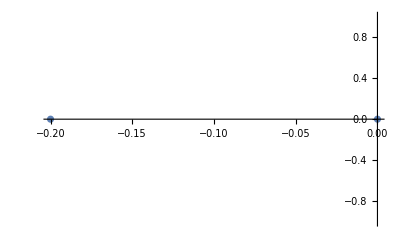

```mathematica
ListPlot[Table[{x,ReleaseHold[f[x]]},{x,-0.2,0.2,0.01}]]
```

```mathematica
l2[[41]]
```

0.3716982507 ⅈ

```mathematica
F[x_]=l2[[1+(x_+0.2)/0.01]]
```

Part::pkspec1: The expression 1+100. (0.2+x_) cannot be used as a part specification.

Rule::rhs: Pattern x_ appears on the right-hand side of rule F[x_]→{2.408485451×10^-11 ⅈ,-5.706973835 ⅈ,-5.29796727 ⅈ,-4.595566286 ⅈ,«34»,-5.609063496 ⅈ,-5.808990222 ⅈ,0.3716982507 ⅈ}⟦1+100. (0.2+x_)⟧.

{2.408485451×10^-11 ⅈ,-5.706973835 ⅈ,-5.29796727 ⅈ,-4.595566286 ⅈ,-3.907878402 ⅈ,-3.285621616 ⅈ,-2.735779221 ⅈ,-2.25472372 ⅈ,-1.836527857 ⅈ,-1.474658243 ⅈ,-1.163270862 ⅈ,-0.8970991409 ⅈ,-0.6707152511 ⅈ,-0.4834373665 ⅈ,-0.3290007418 ⅈ,-0.2058400533 ⅈ,-0.111850247 ⅈ,-0.04536247722 ⅈ,-0.005105310703 ⅈ,0.009826477882 ⅈ,3.645720178×10^-14 ⅈ,-0.03434405729 ⅈ,-0.09327935977 ⅈ,-0.1771178211 ⅈ,-0.2867982648 ⅈ,-0.4231352786 ⅈ,-0.5874133442 ⅈ,-0.7819834887 ⅈ,-1.008464754 ⅈ,-1.269677222 ⅈ,-1.568718372 ⅈ,-1.909182988 ⅈ,-2.295089247 ⅈ,-2.730777185 ⅈ,-3.220334554 ⅈ,-3.766457085 ⅈ,-4.367185531 ⅈ,-5.005417609 ⅈ,-5.609063496 ⅈ,-5.808990222 ⅈ,0.3716982507 ⅈ}⟦1+100. (0.2+x_)⟧

Part::pkspec1: The expression 1+100. (0.2+x) cannot be used as a part specification.

NIntegrate::inumr: The integrand -((0.+1.79282×10^-13 ⅈ) k3 (0.00226531+«48»+k3^9 (3.38422×10^-6+«15») Cos[θ]^9))/((0.863513+«4»+k3 (0.150824+«1») Cos[θ])^2 (0.0460722+«3»+k3 («19»+«19» x) Cos[θ]) «2» («1»)^3 («1»)^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0},{0,6.283185307}}.